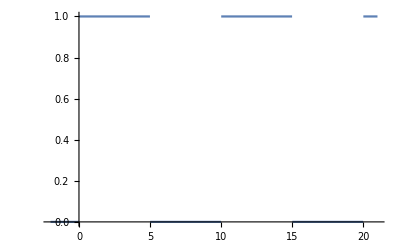

```mathematica
Clear["Global`*"]
squareWave[t_,period_,duty_]:=UnitBox[Mod[t/period,1.]/(2. duty)]
Plot[squareWave[t,10,0.5],{t,-2,21}]
```